```mathematica
1/4+1/3//N
```

0.583333

```mathematica
Together[1/a+1/b]
```

(a+b)/(a b)

```mathematica
ScientificForm[0.00123]
```

1.23×10^-3

```mathematica
a1/2
```

a1/2

```mathematica
Clear@f
```

```mathematica
f[x_]=1+2 x
```

1+2 x

```mathematica
Factor[x^2+2 x+1]
```

(1+x)^2

```mathematica
Manipulate[Expand[(1+x)^n],{n,2,20,1}]
```

```mathematica
Solve[x^2+5 x-6==0,x]
```

{{x→-6},{x→1}}

```mathematica
NSolve[7 x^2+3 x-5==0,x]
```

{{x→-1.08618},{x→0.657611}}

```mathematica
Solve[{x^2+5==y,7 x-5==y},{x,y}]
```

{{x→2,y→9},{x→5,y→30}}

```mathematica
Roots[x^2+3 x-4==0,x]
```

x==-4||x==1

```mathematica
NRoots[360+234 x-1051 x^2+11 x^3+304 x^4-20 x^5==0,x]
```

x==-1.79025||x==-0.498678||x==0.797819||x==1.68398||x==15.0071

```mathematica
NSolve[360+234 x-1051 x^2+11 x^3+304 x^4-20 x^5==0,x]
```

{{x→-1.79025},{x→-0.498678},{x→0.797819},{x→1.68398},{x→15.0071}}

```mathematica
Reduce[{0<x<2,1<=x<=4},x]
```

1≤x<2

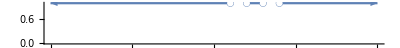

```mathematica
NumberLinePlot[x<1||2<x<3||x>4,{x,-10,10}]
```

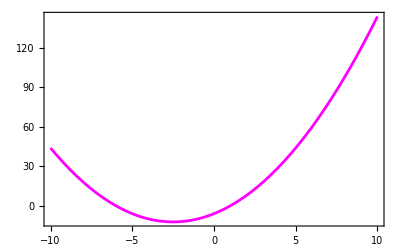

```mathematica
Plot[x^2+5 x-6, {x, -10, 10},Frame->True,PlotStyle->Magenta]
```

```mathematica
Reduce[{x^2+y<2&&x+y<1}]
```

(x≤1/2 (1-√5)&&y<2-x^2)||(1/2 (1-√5)<x≤1/2 (1+√5)&&y<1-x)||(x>1/2 (1+√5)&&y<2-x^2)

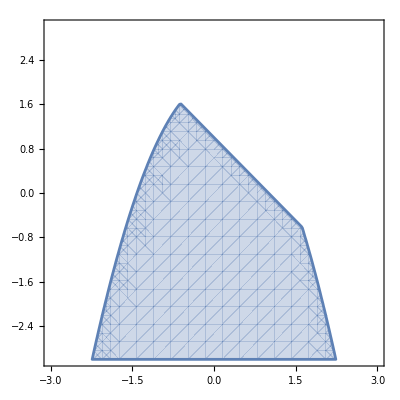

```mathematica
RegionPlot[Reduce[{x^2+y<2&&x+y<1}],{x,-3,3},{y,-3,3}]
```

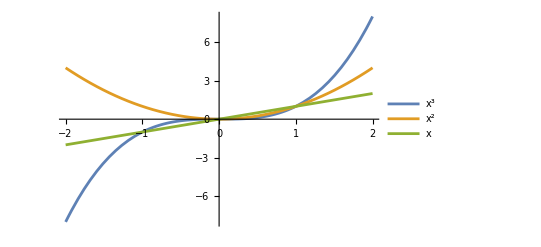

```mathematica
Plot[{x^3,x^2,x},{x,-2,2},PlotLegends->"Expressions"]
```

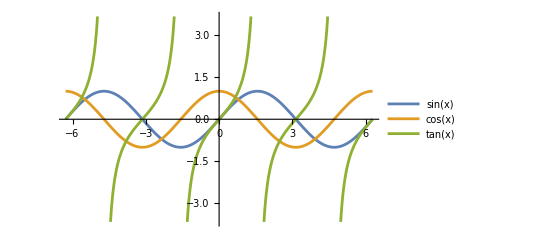

```mathematica
Plot[{Sin@x,Cos@x,Tan@x},{x,-2 π,2 π},PlotLegends->"Expressions"]
```

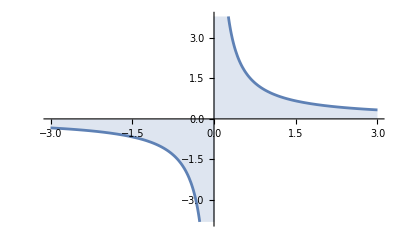

```mathematica
Plot[1/x,{x,-3,3},Filling->Axis]
```

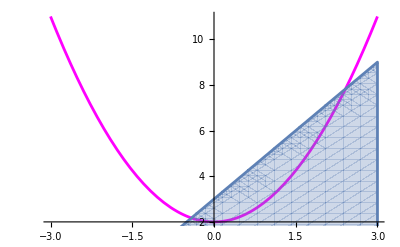

```mathematica
Show[{Plot[x^2+2,{x,-3,3},PlotStyle->Magenta],RegionPlot[2 x>y-3,{x,-3,3},{y,0,9}]}]
```

```mathematica
TrigExpand[Sin[2 x]]
```

2 Cos[x] Sin[x]

```mathematica
Manipulate[PolarPlot[Sin[a θ]+Cos[a θ],{θ,0,2 Pi}],{a,1,50,1}]
```

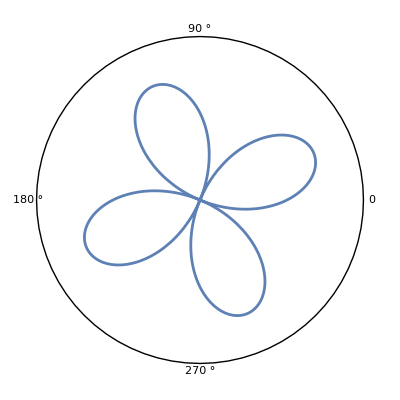

```mathematica
PolarPlot[Sin[2 θ]+Cos[2 θ],{θ,0,2 Pi},PolarAxes->Automatic,PolarTicks->{0 °,90 °,180 °,270 °}]
```

```mathematica
ToPolarCoordinates[{1,1}]
```

{√2,π/4}

```mathematica
FromPolarCoordinates@%
```

{1,1}

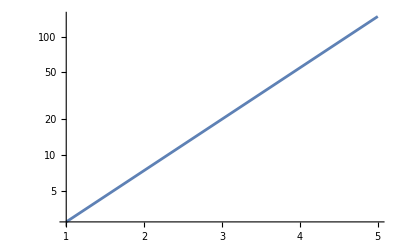

```mathematica
LogPlot[E^x,{x,1,5}]
```

```mathematica
Limit[Sin[x]/x,x->0]
```

1

```mathematica
Simplify[(x^3-1)/(x-1)]
```

1+x+x^2

```mathematica
Limit[(x^3-1)/(x-1),x->1]
```

3

```mathematica
Limit[1/x,x->0,Direction->1]
```

-∞

```mathematica
Limit[1/x,x->0,Direction->-1]
```

∞

```mathematica
TraditionalForm[HoldForm[Limit[1/x,x->Infinity]]]//TeXForm
```

\underset{x\to \infty }{\text{lim}}\frac{1}{x}

```mathematica
D[x^6,x]
```

6 x^5

```mathematica
Sin'[x]
```

Cos[x]

```mathematica
D[Sin@x,x]
```

Cos[x]

```mathematica
f[x_]=x^2+2 x+1;
```

```mathematica
f'[x]
```

2+2 x

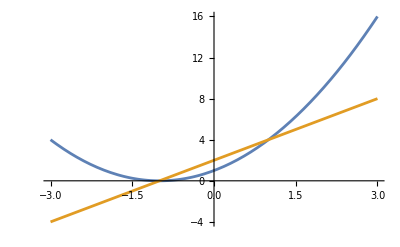

```mathematica
Plot[{f[x],f'[x]},{x,-3,3}]
```

```mathematica
Table[D[Sin[x^2],{x,n}],{n,2,15,1}]//TableForm
```

2 Cos[x^2]-4 x^2 Sin[x^2]
-8 x^3 Cos[x^2]-12 x Sin[x^2]
-48 x^2 Cos[x^2]-12 Sin[x^2]+16 x^4 Sin[x^2]
-120 x Cos[x^2]+32 x^5 Cos[x^2]+160 x^3 Sin[x^2]
-120 Cos[x^2]+480 x^4 Cos[x^2]+720 x^2 Sin[x^2]-64 x^6 Sin[x^2]
3360 x^3 Cos[x^2]-128 x^7 Cos[x^2]+1680 x Sin[x^2]-1344 x^5 Sin[x^2]
13440 x^2 Cos[x^2]-3584 x^6 Cos[x^2]+1680 Sin[x^2]-13440 x^4 Sin[x^2]+256 x^8 Sin[x^2]
30240 x Cos[x^2]-48384 x^5 Cos[x^2]+512 x^9 Cos[x^2]-80640 x^3 Sin[x^2]+9216 x^7 Sin[x^2]
30240 Cos[x^2]-403200 x^4 Cos[x^2]+23040 x^8 Cos[x^2]-302400 x^2 Sin[x^2]+161280 x^6 Sin[x^2]-1024 x^10 Sin[x^2]
-2217600 x^3 Cos[x^2]+506880 x^7 Cos[x^2]-2048 x^11 Cos[x^2]-665280 x Sin[x^2]+1774080 x^5 Sin[x^2]-56320 x^9 Sin[x^2]
-7983360 x^2 Cos[x^2]+7096320 x^6 Cos[x^2]-135168 x^10 Cos[x^2]-665280 Sin[x^2]+13305600 x^4 Sin[x^2]-1520640 x^8 Sin[x^2]+4096 x^12 Sin[x^2]
-17297280 x Cos[x^2]+69189120 x^5 Cos[x^2]-4392960 x^9 Cos[x^2]+8192 x^13 Cos[x^2]+69189120 x^3 Sin[x^2]-26357760 x^7 Sin[x^2]+319488 x^11 Sin[x^2]
-17297280 Cos[x^2]+484323840 x^4 Cos[x^2]-92252160 x^8 Cos[x^2]+745472 x^12 Cos[x^2]+242161920 x^2 Sin[x^2]-322882560 x^6 Sin[x^2]+12300288 x^10 Sin[x^2]-16384 x^14 Sin[x^2]
2421619200 x^3 Cos[x^2]-1383782400 x^7 Cos[x^2]+33546240 x^11 Cos[x^2]-32768 x^15 Cos[x^2]+518918400 x Sin[x^2]-2905943040 x^5 Sin[x^2]+307507200 x^9 Sin[x^2]-1720320 x^13 Sin[x^2]

```mathematica
Integrate[8 x^4,x]
```

(8 x^5)/5

```mathematica
∫8 x^4 ⅆx
```

(8 x^5)/5

```mathematica
∫_0^π Sin[x]ⅆx
```

2

```mathematica
Integrate[x^3 Sin[x]+2 Log[3 x]^2,{x,0,Pi}]
```

π (-6+π^2+2 (2+Log[3]^2+Log[9] (-1+Log[π])+(-2+Log[π]) Log[π]))

```mathematica
NIntegrate[x^3 Sin[x]+2 Log[3 x]^2,{x,0,Pi}]
```

28.1531

```mathematica
Table[Fibonacci[x],{x,1,19}]
```

{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181}

```mathematica
N[4181/2584,20]
```

1.6180340557275541796

```mathematica
N[GoldenRatio,20]
```

1.6180339887498948482

```mathematica
RandomInteger[{1,10}]
```

6

```mathematica
RecurrenceTable[{a[x]==a[x-1]+a[x-2],a[1]==RandomInteger[{1,10}],a[2]==RandomInteger[{1,10}]},a,{x,3,20}]
```

{11,17,28,45,73,118,191,309,500,809,1309,2118,3427,5545,8972,14517,23489,38006}

```mathematica
FindSequenceFunction[%,n]
```

8 Fibonacci[n]+3 LucasL[n]

```mathematica
(8 Fibonacci[n]+3 LucasL[n])/.n->1
```

11

```mathematica
N[Ratios@Take[RecurrenceTable[{a[x]==a[x-1]+a[x-2],a[1]==RandomInteger[{1,10}],a[2]==RandomInteger[{1,10}]},a,{x,3,20}],-2],10][[1]]
```

1.618034019

```mathematica
N[%[[2]]/%[[1]],10]
```

1.618033999

```mathematica
Total[%]
```

159372

```mathematica
∑_(i=1)^∞ 2^(-i)
```

1

```mathematica
∑_(i=1)^∞ 3^(-i)
```

1/2

```mathematica
∑_(i=1)^∞ 4^(-i)
```

1/3

```mathematica
∑_(i=1)^∞ 5^(-i)
```

1/4

```mathematica
sol=DSolve[y'[x]+y[x]==x,y[x],x]
```

{{y[x]→-1+x+ⅇ^-x C[1]}}

```mathematica
caidalibre=NDSolve[{y''[t]==-9.8,y[0]==3,y'[0]==0},y[t],{t,0,5}]
```

{y[t]→InterpolatingFunction[…][t]}

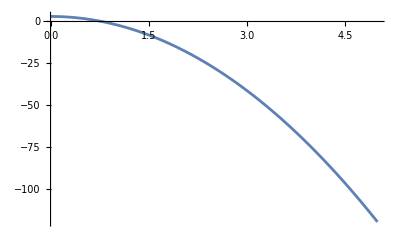

```mathematica
Plot[Evaluate[y[t]/.caidalibre],{t,0,5}]
```

```mathematica
Solve[(Evaluate[y[t]/.caidalibre])==0,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→0.782461}}

```mathematica
caidalibre2=NDSolve[{y''[t]==-9.8,y[0]==3,y'[0]==0,WhenEvent[y[t]==0,tend=t;"StopIntegration"]},y[t],{t,0,5}]
```

{{y[t]→InterpolatingFunction[…][t]}}

```mathematica
tend
```

0.782461

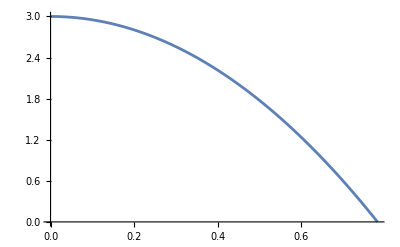

```mathematica
Plot[Evaluate[y[t]/.caidalibre2],{t,0,tend}]
```

```mathematica
NDSolve[{y''[t]==-9.81,y[0]==5,y'[0]==0,WhenEvent[y[t]==0,y'[t]->-0.95y'[t]],WhenEvent[y'[t]==0,Print[t]]},y,{t,0,10}];
```

1.96879

3.83915

5.61598

7.30398

8.90757

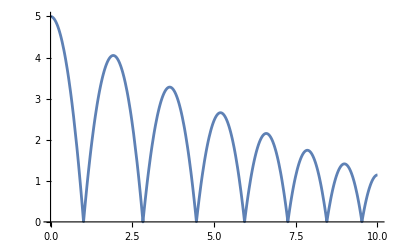

```mathematica
Plot[y[t]/.%,{t,0,10}]
```

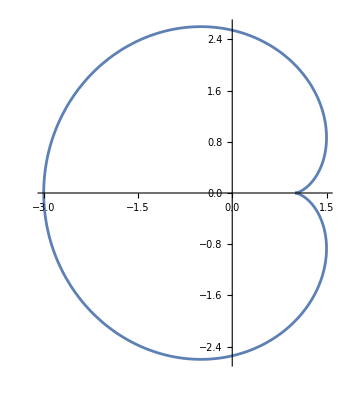

```mathematica
ParametricPlot[{2 Cos[t]-Cos[2 t],2 Sin[t]-Sin[2 t]},{t,0,2 Pi}]
```

```mathematica
Plot3D[Sqrt[x^2+y^2],{x,-1,1},{y,-1,1}]
```

-Graphics3D-

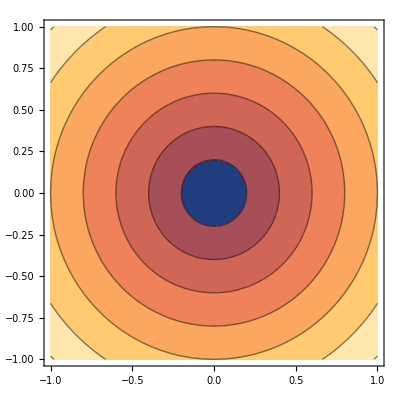

```mathematica
ContourPlot[Sqrt[x^2+y^2],{x,-1,1},{y,-1,1}]
```

```mathematica
DensityPlot[Sqrt[x^2+y^2],{x,-1,1},{y,-1,1}]
```

-Graphics-

```mathematica
Plot3D[x^2-y^2,{x,-3,3},{y,-3,3}]
```

-Graphics3D-

```mathematica
SphericalPlot3D[Sin[θ],{θ,0,Pi},{ϕ,0,2 Pi}]
```

-Graphics3D-

```mathematica
RevolutionPlot3D[x^4-x^2,{x,-1,1}]
```

-Graphics3D-

```mathematica
r[θ_,ω_]=(3/(ω Sin[θ])) Cos[(π+ArcCos[ω Sin[θ]])/3]
```

(3 Cos[1/3 (π+ArcCos[ω Sin[θ]])] Csc[θ])/ω

```mathematica
r[π/2,.999999]
```

1.49878

```mathematica
SphericalPlot3D[r[θ,.99],{θ,0,π},{ϕ,0,2 π},AspectRatio->1,ImageSize->Large]
```

-Graphics3D-